```mathematica
Clear[f]
f[kx_,ky_,m_]=Laplacian[m/(2(kx^2+ky^2+m^2)^(3/2)),{kx,ky}]//FullSimplify
Manipulate[DensityPlot[f[kx,ky,m],{kx,-10,10},{ky,-10,10},PlotPoints->100,PlotRange->Full],{{m,1},0,10}]
```

(9 (kx^2+ky^2) m-6 m^3)/(2 (kx^2+ky^2+m^2)^(7/2))

```mathematica
f[kx,ky,m]/.{kx->k Cos[ϕ],ky->k Sin[ϕ]}//FullSimplify
```

(3 m (3 k^2-2 m^2))/(2 (k^2+m^2)^(7/2))

```mathematica
$Assumptions=m∈Reals;
Integrate[(m k)/(2(k^2+m^2)^(3/2)),{k,0,∞}]//FullSimplify
```

Sign[m]/2

```mathematica
Integrate[(3 m k (3 k^2-2 m^2))/(2 (k^2+m^2)^(7/2)),k]
```

-(3 k^2 m)/(2 (k^2+m^2)^(5/2))

```mathematica
Integrate[(3 m k (3 k^2-2 m^2))/(2 (k^2+m^2)^(7/2)),{k,0,∞}, Assumptions->m∈Reals]
```

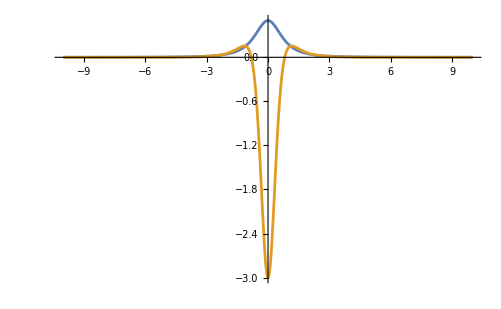

```mathematica
Plot[Evaluate@({m/(2(kx^2+ky^2+m^2)^(3/2)),f[kx,ky,m]}/.{ky->0,m->1}),{kx,-10,10},PlotRange->Full]
```

```mathematica
Clear[kk,xx]
kk[t_]={kx[t],ky[t],kz[t]}
xx[t_]={x[t],y[t],z[t]}
```

{kx[t],ky[t],kz[t]}

{x[t],y[t],z[t]}

```mathematica
ef=-{1,0,0};
x0={0,0,0};
k0={-1,0,0};
ϵ[kx_,ky_,kz_]:=√(kx^2+ky^2+m^2);
v[kx_,ky_,kz_]=Grad[ϵ[kx,ky,kz],{kx,ky,kz}]
v[Sequence@@k0]
Ω[kx_,ky_,kz_]={0,0,m/(2(kx^2+ky^2+m^2)^(3/2))};
corr[kx_,ky_,kz_]=1/2 σ Laplacian[Ω[kx,ky],{kx,ky}]//FullSimplify;
DEQ[x_,y_,z_,kx_,ky_,kz_,t_]=Join[
Table[kk'[t][[i]]==-ef[[i]],{i,Length[kk[t]]}],
Table[xx'[t][[i]]==v[Sequence@@kk[t]][[i]]-Cross[kk'[t],Ω[Sequence@@kk[t]]+corr[Sequence@@kk[t]]][[i]],{i,Length[xx[t]]}],
Table[kk[0][[i]]==k0[[i]],{i,Length[kk[t]]}],
Table[xx[0][[i]]==x0[[i]],{i,Length[xx[t]]}]
];
```

{kx/(√(kx^2+ky^2+m^2)),ky/(√(kx^2+ky^2+m^2)),0}

{-1/(√(1+m^2)),0,0}

```mathematica
DEQ[XX,YY,ZZ,KX,KY,KZ,s]/.{m->0.001}
```

{KX'[s]==1,KY'[s]==0,KZ'[s]==0,XX'[s]==KX[s]/(√(1.×10^-6+KX[s]^2+KY[s]^2))+(1.5×10^-9 σ KY'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))-(0.00225 σ KX[s]^2 KY'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))-(0.00225 σ KY[s]^2 KY'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))-(0.0005 KY'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(3/2)),YY'[s]==KY[s]/(√(1.×10^-6+KX[s]^2+KY[s]^2))-(1.5×10^-9 σ KX'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))+(0.00225 σ KX[s]^2 KX'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))+(0.00225 σ KY[s]^2 KX'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(7/2))+(0.0005 KX'[s])/((1.×10^-6+KX[s]^2+KY[s]^2)^(3/2)),ZZ'[s]==0,KX[0]==-1,KY[0]==0,KZ[0]==0,XX[0]==0,YY[0]==0,ZZ[0]==0}

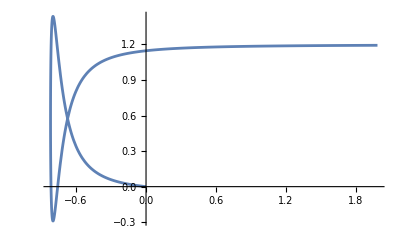

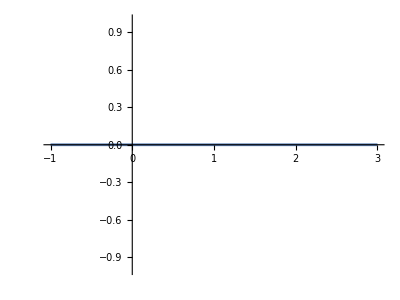

```mathematica
sol={XX[t],YY[t],KX[t],KY[t]}/.First[NDSolve[DEQ[XX,YY,ZZ,KX,KY,KZ,t]/.{m->0.2,σ->0.03},{XX,YY,ZZ,KX,KY,KZ},{t,-10,10}]];
ParametricPlot[Evaluate@(sol[[;;2]]/.t->s),{s,0,4},PlotRange->Full]
ParametricPlot[Evaluate@(sol[[3;;]]/.t->s),{s,0,4},PlotRange->Full]
```